```mathematica
(*2. Introduction*)
(*(a)The syntax of the Mathematica language*)
{FullForm[a*b+c], FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
FullForm[%]
```

Times[a,Plus[b,c]]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c// FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c
```

a^3 b^2 c

```mathematica
∫k[x]ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s+n
```

n+Zeta[s]

```mathematica
(*(b)The Meaning of Expressions*)
Sin[x],f[x,y]
```

```mathematica
Expand[(x+1)^2]
```

1+2 x+x^2

```mathematica
x+y,a=b
```

```mathematica
{a,b,c}
```

{a,b,c}

```mathematica
RGBColor[r,g,b]
```

RGBColor[r,g,b]

```mathematica
(*(c) The four kinds of bracketing in Mathematica*)
v[[ {a,b} ]]
```

Part::pspec: Part specification {a, b} is neither an integer nor a list of integers.

v⟦{a,b}⟧

```mathematica
(*
(term)      parentheses for grouping
f[x]          square brackets for functions
{a,b,c}       curly braces for lists
v[[i]]        double brackets for indexing (Part[v,i])
*)
```

```mathematica
(*(d) Use Brackets and Braces Correctly*)
```

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12, √(9+y),"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,2,{3,4,5},{3,2}}
```

{1,2,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v = Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

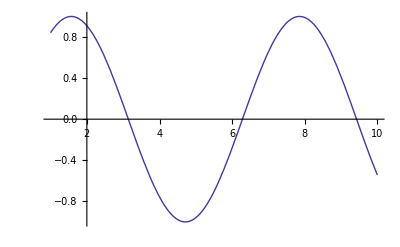

```mathematica
Plot[Sin[x],{x,1,10}]
```

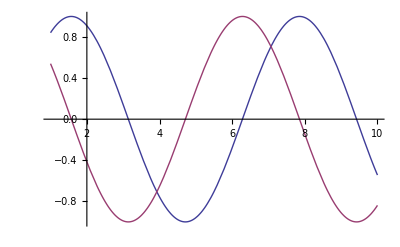

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(2+π
```

```mathematica
(*3. Symbolic Analysis*)
(*(a) Symbolic Computation*)
```

```mathematica
3+62-1
```

64

```mathematica
3x-x+2
```

2+2 x

```mathematica
-1+2x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4x^2
```

x-3 x^2

```mathematica
xy+2x^2y+y^2x^2-2yx
```

xy+2 x^2 y+x^2 y^2-2 yx

```mathematica
(x+2y+1)(x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801(4n)!(1103+26390n)/(n!^4 396^(4n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*(b) Values for Symbols*)
```

```mathematica
1+2x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x->3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y)(x-y)^2/. {x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
x+5-2x
```

6+a-2 (1+a)

```mathematica
x=.
```

```mathematica
x+5-2x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5a
```

1+25 a^2

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
(*(c) Transforming Algebraic Expressions*)
```

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
(*(d) Simplifying Algebraic Expressions*)
```

```mathematica
Simplify[x^2+2x+1]
```

(1+x)^2

```mathematica
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
(*4. Calculus*)
```

```mathematica
(*(a) Differentiation*)
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
D[{{2x,2y},{y,x}}]
```

{{2 x,2 y},{y,x}}

```mathematica
(*(b) Integration*)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Log[1-x^2],x]
```

-2 x-Log[1-x]+Log[1+x]+x Log[1-x^2]

```mathematica
Integrate[Log[1-x^2]/x,x]
```

-1/2 PolyLog[2,x^2]

```mathematica
Integrate[Exp[1-x^2],x]
```

1/2 ⅇ √π Erf[x]

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
Integrate[(1-x^2)^n,x]
```

x Hypergeometric2F1[1/2,-n,3/2,x^2]

```mathematica
Integrate[x^x,x]
```

∫x^x ⅆx

```mathematica
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
N[%]
```

0.783431

```mathematica
Integrate[x^2+y^2,{x,0,1},{y,0,x}]
```

1/3

```mathematica
Integrate[x^10 Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512

```mathematica
(*(c) Indefinite Integrals*)
```

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
D[%,x]
```

-1/(2 (1-x))-1/(2 (1+x))

```mathematica
Simplify[%]
```

1/(-1+x^2)

```mathematica
Integrate[a x^2,x]
```

(a x^3)/3

```mathematica
Integrate[x b[x]^2,b[x]]
```

1/3 x b[x]^3

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[x^-1,x]
```

Log[x]

```mathematica
Integrate[1/(1+a x^2),x]
```

ArcTan[√a x]/(√a)

```mathematica
Integrate[1/(1-b x^2),x]
```

ArcTanh[√b x]/(√b)

```mathematica
%/.b->-a
```

ArcTanh[√-a x]/(√-a)

```mathematica
D[%,x]
```

1/(1+a x^2)

```mathematica
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/(1+x^2),1/(1+x^2)}

```mathematica
Integrate[1/(1+x^2),x]
```

ArcTan[x]

```mathematica
(*(d) Di.0berential Equations*)
```

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
y'[x]+y[x]==1/.%%
```

{True}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y[x] y'[x]==1,y,x]
```

{{y→Function[{x},-√2 √(x+C[1])]},{y→Function[{x},√2 √(x+C[1])]}}

```mathematica
DSolve[{y'[x]==a y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(a x)}}

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[{y''''[x]==y[x],y[0]==y'[0]==0},y[x],x]
```

{{y[x]→ⅇ^-x (-C[1]+ⅇ^(2 x) C[1]-C[2]+ⅇ^x C[2] Cos[x]-2 ⅇ^x C[1] Sin[x]-ⅇ^x C[2] Sin[x])}}

```mathematica
DSolve[y'[x]-x y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
DSolve[y'[x]-x y[x]==1,y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]+ⅇ^(x^2/2) √(π/2) Erf[x/(√2)]}}

```mathematica
DSolve[y''[x]-x y[x]==0,y[x],x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
DSolve[y''[x]-Exp[x] y[x]==0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

```mathematica
DSolve[y''[x]+Cos[x] y[x]==0,y,x]
```

{{y→Function[{x},C[1] MathieuC[0,-2,x/2]+C[2] MathieuS[0,-2,x/2]]}}

```mathematica
DSolve[y''[x]-Cot[x]^2 y[x]==0,y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[1/2,(√5)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[1/2,(√5)/2,Cos[x]]}}

```mathematica
DSolve[x^2 y''[x]+y[x]==0,y[x],x]
```

{{y[x]→√x C[1] Cos[1/2 √3 Log[x]]+√x C[2] Sin[1/2 √3 Log[x]]}}

```mathematica
DSolve[y'''[x]+x y[x]==0,y[x],x]
```

{{y[x]→C[1] HypergeometricPFQ[{},{1/2,3/4},-x^4/64]+(x C[2] HypergeometricPFQ[{},{3/4,5/4},-x^4/64])/(2 √2)+1/8 x^2 C[3] HypergeometricPFQ[{},{5/4,3/2},-x^4/64]}}

```mathematica
DSolve[y'''[x]+Exp[x] y[x]==0,y[x],x]
```

{{y[x]→C[1] HypergeometricPFQ[{},{1,1},-ⅇ^x]+C[2] MeijerG[{{},{}},{{0,0},{0}},-ⅇ^x]+C[3] MeijerG[{{},{}},{{0,0,0},{}},ⅇ^x]}}

```mathematica
DSolve[y'[x]-y[x]^2==0,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
DSolve[y'[x]-y[x]^2==x,y[x],x]//FullSimplify
```

{{y[x]→(√x (-BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1])}}

```mathematica
DSolve[y'[x]-x y[x]^2-y[x]==0,y[x],x]
```

{{y[x]→-ⅇ^x/(-ⅇ^x+ⅇ^x x-C[1])}}

```mathematica
DSolve[y'[x]-x y[x]^3+y[x]==0,y[x],x]
```

{{y[x]→-(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))},{y[x]→(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))}}

```mathematica
DSolve[y'[x]+x y[x]^3+y[x]^2==0,y[x],x]
```

Solve[1/2 ((2 ArcTanh[(-1-2 x y[x])/(√5)])/(√5)+Log[(-1-x y[x] (-1-x y[x]))/(x^2 y[x]^2)])==C[1]-Log[x],y[x]]

```mathematica
DSolve[y'[x]-y[x]==UnitStep[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x (1-ⅇ^-x) UnitStep[x]}}

```mathematica
DSolve[y'[x]+Clip[x] y[x]==0,y[x],x]
```

{{y[x]→ⅇ^Piecewise[{{x, x≤-1}, {-1/2-x^2/2, -1<x≤1}, {-x, True}}] C[1]}}

```mathematica
DSolve[{y'[x]+3 z'[x]==4 y[x]+1/x,y[x]+z[x]==1},{y[x],z[x]},x]
```

{{y[x]→3/2+1/18 (-ⅇ^(-2 x) C[1]-9 ⅇ^(-2 x) (3 ⅇ^(2 x)+ExpIntegralEi[2 x])),z[x]→-1/2+1/18 (ⅇ^(-2 x) C[1]+9 ⅇ^(-2 x) (3 ⅇ^(2 x)+ExpIntegralEi[2 x]))}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y,{x1,x2}]
```

{{y→Function[{x1,x2},(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)]}}

```mathematica
(D[#,x1]+D[#,x2]+D[#,x3])&[y[x1,x2,x3]]==0
```

y^(0,0,1)[x1,x2,x3]+y^(0,1,0)[x1,x2,x3]+y^(1,0,0)[x1,x2,x3]==0

```mathematica
DSolve[%,y[x1,x2,x3],{x1,x2,x3}]
```

{{y[x1,x2,x3]→C[1][-x1+x2,-x1+x3]}}

```mathematica
(c^2 D[#,x,x]-D[#,t,t])&[y[x,t]]==0
```

General::ivar: 1 + x^2 is not a valid variable.

-∂_(1+x^2,1+x^2) y[x,1+x^2]+c^2 (2 y^(0,1)[x,1+x^2]+2 x y^(1,1)[x,1+x^2]+2 x (2 x y^(0,2)[x,1+x^2]+y^(1,1)[x,1+x^2])+y^(2,0)[x,1+x^2])==0

```mathematica
DSolve[%,y[x,t],{x,t}]
```

DSolve::dsvar: 1 + x^2 cannot be used as a variable.

DSolve[-∂_(1+x^2,1+x^2) y[x,1+x^2]+c^2 (2 y^(0,1)[x,1+x^2]+2 x y^(1,1)[x,1+x^2]+2 x (2 x y^(0,2)[x,1+x^2]+y^(1,1)[x,1+x^2])+y^(2,0)[x,1+x^2])==0,y[x,1+x^2],{x,1+x^2}]

```mathematica
DSolve[x1 D[y[x1,x2],x1]+x2 D[y[x1,x2],x2]==Exp[x1 x2],y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→1/2 (ExpIntegralEi[x1 x2]+2 C[1][x2/x1])}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==Exp[y[x1,x2]],y[x1,x2],{x1,x2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x1,x2]→-Log[-x1-C[1][-x1+x2]]}}

```mathematica
DSolve[D[y[x1,x2],x1] D[y[x1,x2],x2]==a,y[x1,x2],{x1,x2}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{y[x1,x2]→C[1]+(a x1)/C[2]+x2 C[2]}}

```mathematica
(*5. Plotting*)
(*(a) How to plot a graph*)
```

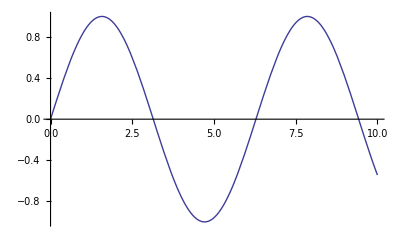

```mathematica
Plot[Sin[x],{x,0,10}]
```

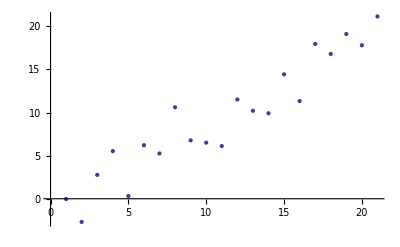

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

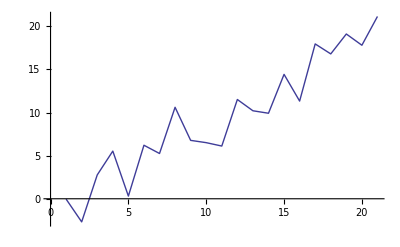

```mathematica
ListLinePlot[datapts]
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]
```

-Graphics-

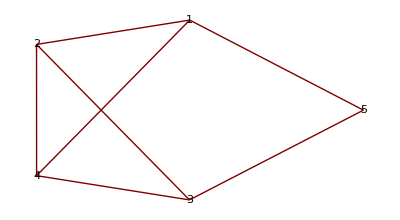

```mathematica
GraphPlot[{1->2,1->4,2->4,3->4,3->2,3->5,5->1},VertexLabeling->True]
```

```mathematica
(*(b) How to plot functions of one variable*)
```

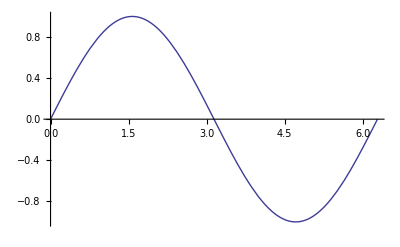

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

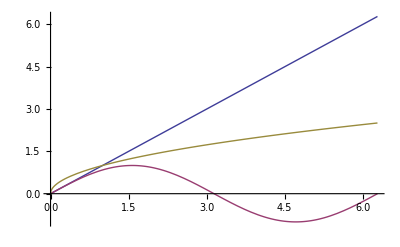

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

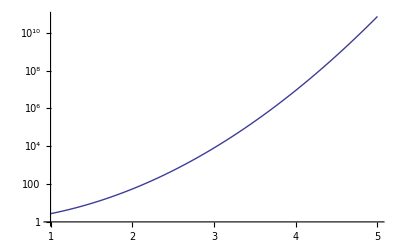

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

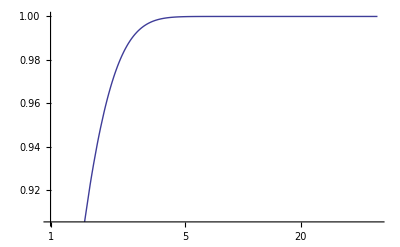

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

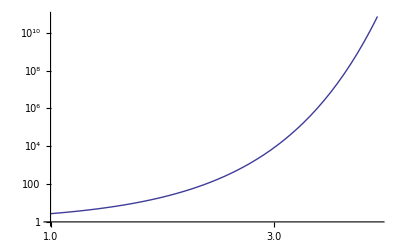

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

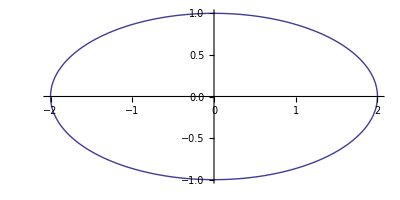

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

General::ivar: 1 + x^2 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

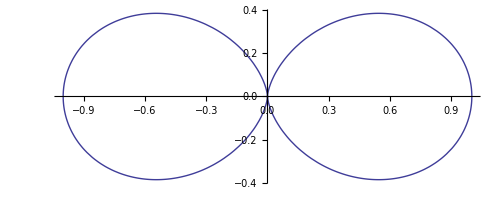

```mathematica
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

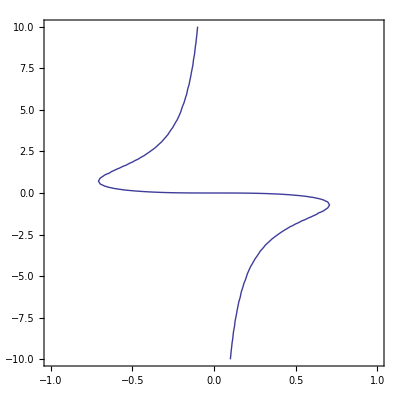

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```

```mathematica
(*(c) How to plot parametric functions*)
```

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

-Graphics-

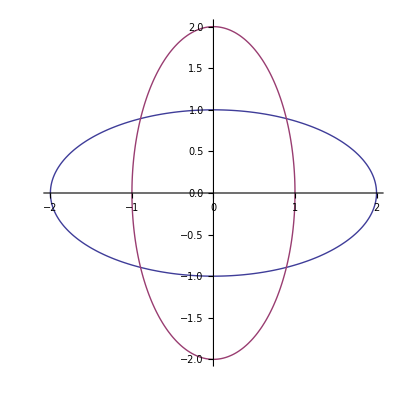

```mathematica
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]}},{t,0,2 Pi}]
```

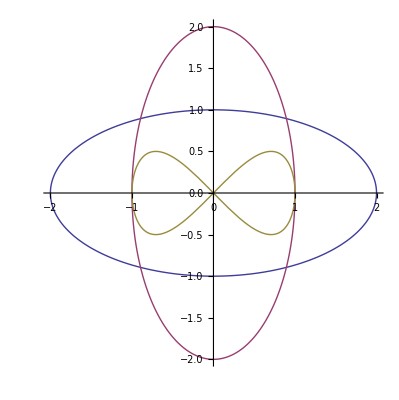

```mathematica
ParametricPlot[
{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]},{Sin[t],Sin[t] Cos[t]}},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],Log[r^(1/2)]},{r,0.1,1},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

```mathematica
(*(d) How to plot the results of NDSolve*)
```

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

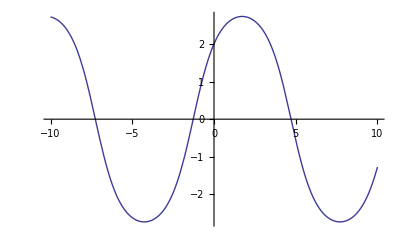

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

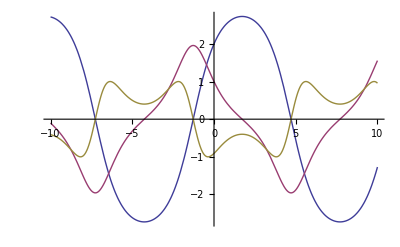

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

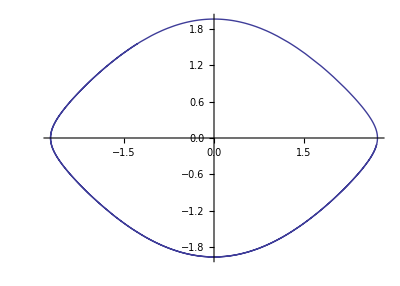

```mathematica
ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,-10,10}]
```

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
wws= 
NDSolve[{D[u[t,x], t,t]==D[u[t,x], x,x]+(1 - u[t, x]^2) (1+2 u[t, x]),u[0, x]== e^-x^2, 
       Derivative[1,0][u][0, x]== 0, u[t, -10]== u[t, 10]},u, {t, 0, 10}, {x, -10, 10}]
```

General::ivar: 1 + x^2 is not a valid variable.

NDSolve::dsvar: 1 + x^2 cannot be used as a variable.

NDSolve[{∂_(1+x^2,1+x^2) u[1+x^2,x]==(1+2 u[1+x^2,x]) (1-u[1+x^2,x]^2)+u^(0,2)[1+x^2,x]+2 u^(1,0)[1+x^2,x]+2 x u^(1,1)[1+x^2,x]+2 x (u^(1,1)[1+x^2,x]+2 x u^(2,0)[1+x^2,x]),u[0,x]==e^(-x^2),u^(1,0)[0,x]==0,u[1+x^2,-10]==u[1+x^2,10]},u,{1+x^2,0,10},{x,-10,10}]

```mathematica
Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

General::ivar: 100.971 is not a valid variable.

NDSolve::dsvar: 100.971 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 », u, {100.971, 0, 10}, {-9.99857, -10, 10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 100.971 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 100.971 is not a valid variable.

NDSolve::dsvar: 100.971 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[« 1 », u, {100.971, 0, 10}, {-9.99857, -10, 10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 100.971 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
DensityPlot[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

General::ivar: 100.971 is not a valid variable.

NDSolve::dsvar: 100.971 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{« 1 »}, u, {100.971, 0, 10}, {-9.99857, -10, 10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 100.971 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 100.971 is not a valid variable.

NDSolve::dsvar: 100.971 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{« 1 »}, u, {100.971, 0, 10}, {-9.99857, -10, 10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 100.971 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
plots=Table[Plot[u[t,x]/.wws,{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
```

General::ivar: 100.992 is not a valid variable.

NDSolve::dsvar: 100.992 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{∂_100.9918287383592`, 100.9918287383592` u[100.9918287383592`, -9.99959142857143`] == (1 + Times[« 2 »]) (1 + Times[« 2 »]) + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 100.992 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 92.9955 is not a valid variable.

NDSolve::dsvar: 92.9955 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 85.3324 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

```mathematica
ListAnimate[plots]
```

```mathematica
bg = 
NDSolve[{D[u[t], t,t] ==  (1 - u[t]^2) (1 + 2 u[t]), u[0] ==  0, u'[0] ==  0},u, {t, 0, 10}]
```

General::ivar: 1 + x^2 is not a valid variable.

NDSolve::dsvar: 1 + x^2 cannot be used as a variable.

NDSolve[{∂_(1+x^2,1+x^2) u[1+x^2]==(1+2 u[1+x^2]) (1-u[1+x^2]^2),u[0]==0,u'[0]==0},u,{1+x^2,0,10}]

```mathematica
plots=Table[Plot[(u[t,x]/.wws)-(u[t]/.bg),{x,-10,10},PlotRange->{-2,2}],{t,0,10,.25}];
```

General::ivar: 100.992 is not a valid variable.

NDSolve::dsvar: 100.992 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{∂_100.9918287383592`, 100.9918287383592` u[100.9918287383592`, -9.99959142857143`] == (1 + Times[« 2 »]) (1 + Times[« 2 »]) + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 100.992 is not a valid variable.

NDSolve::dsvar: 100.992 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{∂_100.9918287383592`, 100.9918287383592` u[100.9918287383592`] == (1 + 2 u[« 1 »]) (1 - Power[« 2 »]), u[0] == 0, SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 100.992 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{∂_100.9918287383592`, 100.9918287383592` u[100.9918287383592`] == (1.`  + 2.` u[« 1 »]) (1.`  - 1.` Power[« 2 »]), u[0.`] == 0.`, SuperscriptBox[
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 92.9955 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

```mathematica
ListAnimate[plots]
```

```mathematica
(*6. Manipulate*)
```

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],
{n1,1,20},{n2,1,20}]
```

```mathematica
Manipulate[
Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20}]
```

```mathematica
Manipulate[n,{n,1,20,1}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20,1}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,300,1}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],
{n,1/2,1/3,1/144},{m,1/2,1/3,1/144}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,a,10 a,a/12},{m,a,10 a,a/12}]
```

```mathematica
Manipulate[
Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},
Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Frame->frame,PlotRange->2],{n1,1,20},{n2,1,20},{frame,{True,False}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},
Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,2,1,0,-1,-2},
ControlType->SetterBar}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},
Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1},ControlType->Manipulator}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},
Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,2,1.5,1,0.5,0,-0.5,-1,-1.5,-2}},{filling,-2,2}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},
{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],
{n1,1,4},{a1,0,1},{p1,0,2 Pi},
{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{{a1,1},0,1},{p1,0,2 Pi},{{n2,5/4},1,4},{{a2,1},0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{n2,5/4,"Frequency 2"},1,4},Delimiter,{{a1,1,"Amplitude 1"},0,1},{{a2,1,"Amplitude 2"},0,1},Delimiter,{{p1,0,"Phase 1"},0,2 Pi},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],"Horizontal",{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,"Vertical",{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```